# FIST 2,2:

```mathematica
Format[g1]:=Subscript[γ,1];Format[g2]:=Subscript[γ,2];Format[be1]:=Subscript[β,1];Format[mu]:=
μ;Format[La]:=Λ;Format[La2]:=Subscript[Λ,2];Format[La1]:=Subscript[Λ,1];Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];
Format[be12]:=Subscript[β,12];Format[be21]:=Subscript[β,21];Format[be2]:=Subscript[β,2];
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];reaProd = compToAsso;
```

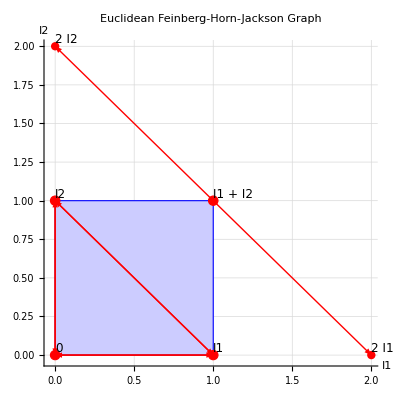

<|Species→{I1,I2},Reactions→{{0,I1},{0,I2},{I1+I2,2 I1},{I1+I2,2 I2},{I1,I2},{I2,I1},{I1,0},{I2,0}},Endotactic→False,StronglyEndotactic→False,OneEndotacticReport→{I1→False,I2→False},FailingSpeciesDirections→{I1,I2},EndotacticDirections→{{-1,0},{0,-1},{1/(√2),1/(√2)},{-1/(√2),-1/(√2)}}|>

Species: {I1,I2}

Deficiency: {δ = Nc - ℓ - s,Nc = 6 (complexes), ℓ = 2 (linkage classes), s = 2 (stoich dimension),δ = 6 - 2 - 2 = 2}

```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels"}]];<<EpidCRN`;
RN = {
  0 -> "I1",0 -> "I2",
  "I2" + "I1" -> 2*"I1",
  "I2" + "I1" -> 2*"I2",
  "I1" -> "I2",
  "I2" -> "I1",
  "I1" -> 0,
  "I2" -> 0
};
endo[RN]
{spe, al, be, gamma, Rv, RHS, def} = extMat[RN]; 
 Print["Species: ", spe]; 
 Print["Deficiency: ", def];
```

```mathematica
(*{RH,spe}=Take[reaToRHS[RN],2];*)cg={g1->0,g2->0};
{al,be,ga,spe}=stoichiometricMatrices[RN];var=ToExpression[spe];
Print["ga, be are",ga//MatrixForm,
be//MatrixForm]
rts={La1, La2, be12 I1 I2,be21 I2 I1,g1 I1, g2 I2,mu1 I1,
mu2 I2};
RHS=ga.rts//FullSimplify;
Print["RHS= ", RHS//MatrixForm," has par",par=Par[RHS,var]]
jac=Grad[RHS,var];jac//MatrixForm

cp=Thread[par>0];cp[[3]]=g1>=0;cp[[4]]=g2>=0;cp
cv=Thread[var>=0];ct=Join[cp,cv];
mS=minSiph[spe,asoRea[RN]];
Print["minimal siphon ",mS, " Check siphon=",isSiph[ToString/@var,asoRea[RN],#]&/@mS]

(*Find all invariant facets*)
iF=invFacet[RN,6];
Print["Invariant facets are:"];
Do[Print[iF[[i]]],{i,Length[iF]}];
cDFE={I1->0,I2->0};cI1={I2->0};cI2={I1->0};csym={be21->be12};
eq=Thread[RHS==0];eqp=Join[eq,ct];
sos=reCL[Reduce[(eqp/.csym),var]/. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n]]//FullSimplify
```

ga, be are(1 | 0 | 1 | -1 | -1 | 1 | -1 | 0
0 | 1 | -1 | 1 | 1 | -1 | 0 | -1)(1 | 0 | 2 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 2 | 1 | 0 | 0 | 0)

RHS= (γ_2 I2+Λ_1-I1 (γ_1-β_12 I2+β_21 I2+μ_1)
γ_1 I1+Λ_2-I2 (γ_2+β_12 I1-β_21 I1+μ_2)) has par{β_12,β_21,γ_1,γ_2,Λ_1,Λ_2,μ_1,μ_2}

(-γ_1+β_12 I2-β_21 I2-μ_1 | γ_2-(-β_12+β_21) I1
γ_1-(β_12-β_21) I2 | -γ_2-β_12 I1+β_21 I1-μ_2)

{β_12>0,β_21>0,γ_1≥0,γ_2≥0,Λ_1>0,Λ_2>0,μ_1>0,μ_2>0}

minimal siphon {} Check siphon={}

Invariant facets are:

γ_2≥0&&γ_1≥0&&I1==(γ_2 (Λ_1+Λ_2)+Λ_1 μ_2)/(γ_2 μ_1+(γ_1+μ_1) μ_2)&&I2==(γ_1 I1+Λ_2)/(γ_2+μ_2)

```mathematica
so=reCL[Reduce[(eqp/.cg),var]/. Subscript[EpidCRN`Private`k, n_] :> 
Subscript[k, n]]//FullSimplify;Print["The cg system admits ", so//Length, " solutions"]
so[[2]]
so[[1]]//FullSimplify
```

The cg system admits 2 solutions

((0<β_12<β_21&&2 I1+μ_2/(β_12-β_21)+√((Λ_1+Λ_2)^2/μ_1^2+(2 (Λ_1-Λ_2) μ_2)/((β_12-β_21) μ_1)+μ_2^2/(β_12-β_21)^2)==(Λ_1+Λ_2)/μ_1)||(β_12>β_21&&(Λ_1+Λ_2)/μ_1+√((Λ_1+Λ_2)^2/μ_1^2+(2 (Λ_1-Λ_2) μ_2)/((β_12-β_21) μ_1)+μ_2^2/(β_12-β_21)^2)==2 I1+μ_2/(β_12-β_21)))&&I2==(-Λ_1+I1 μ_1)/(β_12 I1-β_21 I1)

β_12==β_21&&I1==Λ_1/μ_1&&I2==Λ_2/(β_12 I1-β_21 I1+μ_2)

```mathematica
RHS/.cg//FullSimplify//MatrixForm
so=reCL[Solve[(eq/.cg),var]/. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n]];
```

(be12 I1 I2+La1-I1 (be21 I2+mu1)
La2-I2 (be12 I1-be21 I1+mu2))

The system admits 2 solutions

{{I1→(be12 La1-be21 La1+be12 La2-be21 La2-mu1 mu2-√(4 La1 (be12 mu1-be21 mu1) mu2+(-be12 La1+be21 La1-be12 La2+be21 La2+mu1 mu2)^2))/(2 (be12 mu1-be21 mu1)),I2→-1/mu2(-La1-La2+(be12 La1 mu1)/(2 (be12 mu1-be21 mu1))-(be21 La1 mu1)/(2 (be12 mu1-be21 mu1))+(be12 La2 mu1)/(2 (be12 mu1-be21 mu1))-(be21 La2 mu1)/(2 (be12 mu1-be21 mu1))-(mu1^2 mu2)/(2 (be12 mu1-be21 mu1))-(mu1 √(4 La1 (be12 mu1-be21 mu1) mu2+(-be12 La1+be21 La1-be12 La2+be21 La2+mu1 mu2)^2))/(2 (be12 mu1-be21 mu1)))},{I1→1/(2 (be12 mu1-be21 mu1))(be12 La1-be21 La1+be12 La2-be21 La2-mu1 mu2+√(4 La1 (be12 mu1-be21 mu1) mu2+(-be12 La1+be21 La1-be12 La2+be21 La2+mu1 mu2)^2)),I2→-1/mu2(-La1-La2+(be12 La1 mu1)/(2 (be12 mu1-be21 mu1))-(be21 La1 mu1)/(2 (be12 mu1-be21 mu1))+(be12 La2 mu1)/(2 (be12 mu1-be21 mu1))-(be21 La2 mu1)/(2 (be12 mu1-be21 mu1))-(mu1^2 mu2)/(2 (be12 mu1-be21 mu1))+(mu1 √(4 La1 (be12 mu1-be21 mu1) mu2+(-be12 La1+be21 La1-be12 La2+be21 La2+mu1 mu2)^2))/(2 (be12 mu1-be21 mu1)))}}

```mathematica
so=reCL[Solve[(eq/.csym),var]/. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n]]//FullSimplify;
Print["The system admits ", so//Length, " solutions"]
var2=var/.so[[2]];
var3=var/.so[[3]];Timing[re=reCL[Reduce[Join[cp,Thread[var2 >=0],Thread[var3 >=0]]]//FullSimplify]]
```

The system admits 3 solutions

{0.34375,(γ_2==0&&((γ_1==0&&(0<β_1<(β_2 μ_1)/μ_2||β_1>(β_2 μ_1)/μ_2)&&2 Λ≥(μ μ_1)/β_1+(μ (μ_2+√((β_2 μ_1-β_1 μ_2)^2/β_1^2)))/β_2)||(β_1==(β_2 (γ_1+μ_1))/μ_2&&2 Λ+√((β_2 μ (γ_1+μ_1)-β_1 μ μ_2)^2/(β_1^2 β_2^2))≥(μ (γ_1+μ_1))/β_1+(μ μ_2)/β_2)||((μ (γ_1+μ_1))/β_1+(μ μ_2)/β_2+√((β_2 μ (γ_1+μ_1)-β_1 μ μ_2)^2/(β_1^2 β_2^2))==2 Λ&&((β_2 μ_1)/μ_2<β_1<(β_2 (γ_1+μ_1))/μ_2||0<β_1<(β_2 μ_1)/μ_2))||(2 Λ≥(μ (γ_1+μ_1))/β_1+(μ μ_2)/β_2+√((β_2 μ (γ_1+μ_1)-β_1 μ μ_2)^2/(β_1^2 β_2^2))&&β_1>(β_2 (γ_1+μ_1))/μ_2)))||(γ_1==0&&((β_1==(β_2 μ_1)/(γ_2+μ_2)&&2 Λ≥(μ μ_1)/β_1+(μ (γ_2+μ_2-√((β_2 μ_1-β_1 (γ_2+μ_2))^2/β_1^2)))/β_2)||(2 Λ==(μ μ_1)/β_1+(μ (γ_2+μ_2+√((β_2 μ_1-β_1 (γ_2+μ_2))^2/β_1^2)))/β_2&&(β_1>(β_2 μ_1)/μ_2||(β_2 μ_1)/(γ_2+μ_2)<β_1<(β_2 μ_1)/μ_2))||(β_1<(β_2 μ_1)/(γ_2+μ_2)&&(μ (β_2 μ_1+β_1 (γ_2+μ_2)+Abs[β_2 μ_1-β_1 (γ_2+μ_2)]))/(β_1 β_2)≤2 Λ)))||(2 Λ==(μ (γ_1+μ_1))/β_1+(μ (γ_2+μ_2+√((β_2^2 (γ_1+μ_1)^2)/β_1^2+(γ_2+μ_2)^2+(2 β_2 (γ_1 (γ_2-μ_2)-μ_1 (γ_2+μ_2)))/β_1)))/β_2&&(0<β_1<(β_2 μ_1)/μ_2||β_1>(β_2 μ_1)/μ_2))}

```mathematica
Timing[fi=FindInstance[Join[cp,Thread[var2 >0],Thread[var3 >0](*,{g1>0,g2>0}*)],par]]
```

{0.515625,{}}

```mathematica
soN=Solve[(eq/.fi),var]//N
```

{}

$Aborted

### Computations of R0 using our script:

```mathematica
mod={RHS,var,par};
inf=Range[2,3];
ng=NGM[mod,inf];M=ng[[1]];
K=ng[[6]]//FullSimplify/. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n];K//MatrixForm
Print[" eigs of K are",Apart[(K/.cg)//Eigenvalues//FullSimplify]]
```

((β_1 (γ_2+μ_2) S)/(γ_2 μ_1+(γ_1+μ_1) μ_2) | (β_1 γ_2 S)/(γ_2 μ_1+(γ_1+μ_1) μ_2)
(β_2 γ_1 S)/(γ_2 μ_1+(γ_1+μ_1) μ_2) | (β_2 (γ_1+μ_1) S)/(γ_2 μ_1+(γ_1+μ_1) μ_2))

eigs of K are{(β_2 S)/μ_2,(β_1 S)/μ_1}